```mathematica
X0=0;
```

```mathematica
X1=1;
```

```mathematica
Y0=0;
```

```mathematica
Y1=1;
```

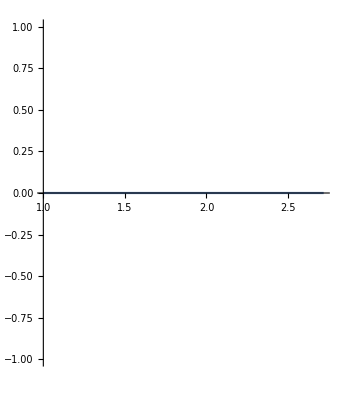

```mathematica
P1=ParametricPlot[{Exp[X]*Cos[Y0],Exp[X]*Sin[Y0]},{X,X0,X1}]
```

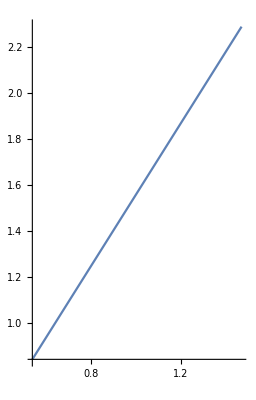

```mathematica
P2=ParametricPlot[{Exp[X]*Cos[Y1],Exp[X]*Sin[Y1]},{X,X0,X1}]
```

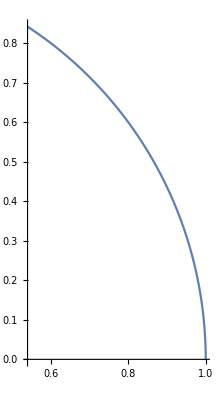

```mathematica
P3=ParametricPlot[{Exp[X0]*Cos[Y],Exp[X0]*Sin[Y]},{Y,Y0,Y1}]
```

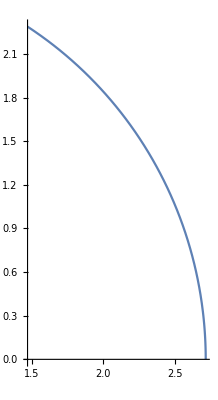

```mathematica
P4=ParametricPlot[{Exp[X1]*Cos[Y],Exp[X1]*Sin[Y]},{Y,Y0,Y1}]
```

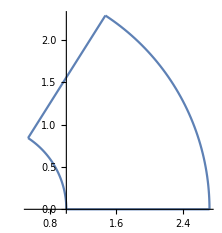

```mathematica
Show[P1,P2,P3,P4,PlotRange->All]
```

f(z)=E^z

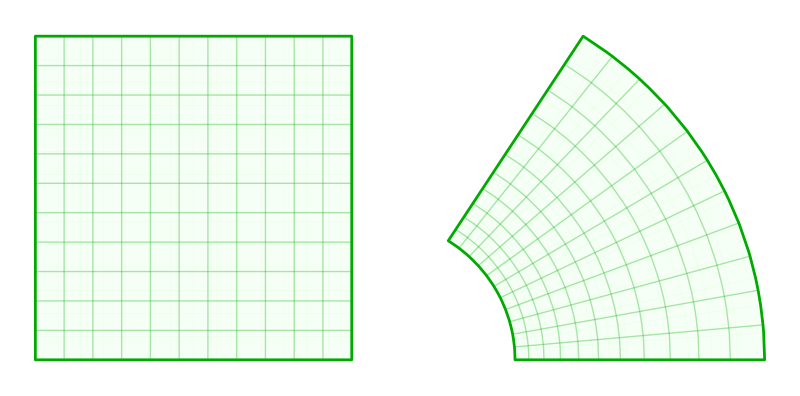

```mathematica
{fig1,fig2}=With[{z=x+I*y},ParametricPlot[ReIm[#],{x,0,1},{y,0,1},Mesh->10,PlotStyle->LightGreen,MeshStyle->Directive[Thick,Darker[Green]],BoundaryStyle->Directive[Thickness[.005],Darker[Green]],Frame->False,Axes->False]]&/@{z,E^z};
GraphicsRow[{fig1,fig2}]
```

```mathematica
x=ⅇ^(1/2 π (-1+X)) Cos[(π Y)/2];
y=ⅇ^(1/2 π (-1+X)) Sin[(π Y)/2];
```

```mathematica
ParametricPlot[{x,y}, {X,0,1},{Y,0,1},PlotRange->All,PlotStyle->Blue];
ParametricPlot[{X,Y}, {X,0,1},{Y,0,1},PlotRange->All,PlotStyle->Gray];
RefCur=Show[%%,%];
```

```mathematica
Manipulate[Show[RefCur,ListPlot[Evaluate[{{x,y},{X,Y}}/.{X-> a,Y-> b}],PlotStyle->PointSize[Large]]],{a,0,1},{b,0,1}]
```

```mathematica
有限元的结果如下：生成不了目标曲面。
尝试根据形状控制方案计算一个G出来？根据以往的经验，这个G就是变形梯度张量。
程序出错了，使用了坐标，而不是状态变量
```

Debug之后

变形梯度张量

```mathematica
F={{D[x,X],D[x,Y]},{D[y,X],D[y,Y]}}
```

{{1/2 ⅇ^(1/2 π (-1+X)) π Cos[(π Y)/2],-1/2 ⅇ^(1/2 π (-1+X)) π Sin[(π Y)/2]},{1/2 ⅇ^(1/2 π (-1+X)) π Sin[(π Y)/2],1/2 ⅇ^(1/2 π (-1+X)) π Cos[(π Y)/2]}}

利用F = AG 求A

```mathematica
G={{√(D[x,X]^2+D[y,X]^2),0},{0,√(D[x,X]^2+D[y,X]^2)}};
Simplify[G,0<X<1&&0<Y<1]
```

{{1/2 ⅇ^(1/2 π (-1+X)) π,0},{0,1/2 ⅇ^(1/2 π (-1+X)) π}}

```mathematica
A=F.Inverse[G]//Simplify
```

{{(ⅇ^(1/2 π (-1+X)) Cos[(π Y)/2])/(√(ⅇ^(π (-1+X)))),-(ⅇ^(1/2 π (-1+X)) Sin[(π Y)/2])/(√(ⅇ^(π (-1+X))))},{(ⅇ^(1/2 π (-1+X)) Sin[(π Y)/2])/(√(ⅇ^(π (-1+X)))),(ⅇ^(1/2 π (-1+X)) Cos[(π Y)/2])/(√(ⅇ^(π (-1+X))))}}

可见这个A就是一个旋转张量

```mathematica
A.Transpose[A]//Simplify
```

{{1,0},{0,1}}